## Ackermann

```mathematica
order=5;
```

```mathematica
Flow[f_,t_,x_, L, order___:2]:= Module[{s},
H[0]=L;
H[1]=f'[L]^t ;
Do[
H[max]=First[r[t]/.RSolve[{r[0]==0,r[t]== Sum[Derivative[k][f][L]BellY[max,k,Table[H[j]/.t->t-1,{j,max}]],{k,2,max}]+ f'[L] r[t-1]},r[t],t]],
{max,2,order}];
s=Sum[1/k! H[k](x-L)^k,{k,0,order}]
(*{{Hyperbolic->s},{Parabolic->Limit[s,{f'[L]->1}]}}*)
];

(* Ackermann function *)
φ[m_,n_,0]:=m+n;
φ[m_,n_,1]:=m n;
φ[m_,n_,2]:=m^n;
φ[m_,0,p_]:=m/;p>2;
φ[u_,v_,p_]:=Flow[φ[u,v,p-1] /.x->1]/;p>2;
```

```mathematica
Quit[];
```

## Flow

```mathematica
flow=Flow[f,t,x, L, 10];
```

```mathematica
l = Conjugate[N[-ProductLog[-Log[E]]/Log[E],300]];
```

```mathematica
Save["C:\\Users\\Owner\\OneDrive\\Documents\\Flow\\Flow\\hyperbolic.txt",flow]
```

```mathematica
flow=Get["C:\\Users\\Owner\\OneDrive\\Documents\\Flow\\Flow\\hyperbolic.txt"];
```

```mathematica
TetrationE= N[flow /.x->1/.f->Exp /. L-> Conjugate[N[-ProductLog[-Log[E]]/Log[E],300]],300];
```

```mathematica
TetrationE/.t->0
```

1.+0. ⅈ

```mathematica
(TetrationE/.t->1)-E
```

3.922562032202252145306103269048017386202633782483307292381601548136535295871413011944366590838805186316914158513758987597057605385379195268406211315546221115429259623218663682522907844671937008325059044618663030785052617604769783476176062116718100847773470227609719078142131559332852492×10^-7-3.1390562145484518050495715654259285802722395509453289587985337436811779452291647669686864550806758829542735462688113082782062109713270205360746253585176091707656542859086204004192585559809545564755981723361669963712065133494732456452796784858019255543515098346100660305728626201398851435×10^-6 ⅈ

```mathematica
(TetrationE/.t->.5)
```

1.53737-0.263834 ⅈ

```mathematica
g[x_]:=Sqrt[2]^x;
TetrationSqrt2= flow /.f->g/.x->1/. L-> 2.`300;
```

```mathematica
(TetrationSqrt2/.t->0)
```

1.

```mathematica
(TetrationSqrt2/.t->1)
```

1.414213562373516971276908599150069106361338465622393656540244997093344036798164508022508066371058957994595006008895932935502149403057870684057625130502422204014381322681209191634251691409295466885888161066130944631708245096510462097819179943332752896208345792737508868517802995014244343573240740795

```mathematica
(TetrationSqrt2/.t->.5)
```

1.24362

```mathematica
%^2
```

2.00000000000119337697345212453677377038030300749170136334801834534987283341538899017273424895170260627340945305761284108022179890131688956099801852837483822506500534823612178172770845775907173241214430840478240088463406600948651901969061628704113571281221624143959130663091819123352649721092959678

```mathematica
Limit[TetrationSqrt2,{t->∞}]
```

2.

```mathematica
Quit[];
```

### Base 2

```mathematica
flow=Get["C:\\Users\\Owner\\OneDrive\\Documents\\Flow\\Flow\\hyperbolic.txt"];
```

```mathematica
g[x_]:=2^x;
Tetration2= flow /.f->g/.x->1/. L->  Conjugate[N[-ProductLog[-Log[2]]/Log[2],100]];
```

```mathematica
tetra[u_]:=Tetration2 /. t->u
```

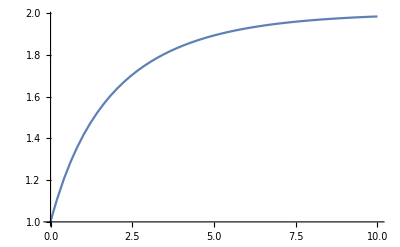

```mathematica
Plot[TetrationSqrt2,{t,0,10}]
```

```mathematica
tetra[0]
```

```mathematica
Table[Tetration2,{t,0,2,.25}]
```

{1.-9.88488×10^-14 ⅈ,1.17569-0.0317369 ⅈ,1.44758-0.0845244 ⅈ,1.75676-0.0486228 ⅈ,2.+7.2046×10^-8 ⅈ,2.28304-0.0689325 ⅈ,2.78487-0.148076 ⅈ,3.40549-0.0672017 ⅈ,4.12718-0.0367672 ⅈ}

```mathematica
s=Normal[Series[Sin[x],{x,0,20}]]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000-x^19/121645100408832000

```mathematica
s
```

x-x^3/6+x^5/120+O[x]^6

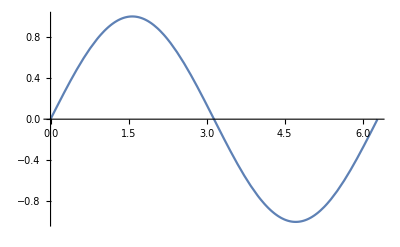

```mathematica
Plot[s,{x,0,2π}]
```

```mathematica
g[x_]:=Sqrt[2]^x;
TetrationSqrt2= flow /.f->g/.x->1/. L-> 2.`300;
```

```mathematica
N[-ProductLog[-1]]
```

0.318132-1.33724 ⅈ

```mathematica
FileNameJoin[{"dir1","dir2","file"}]
```

```mathematica
flow=Get["C:\\Users\\Owner\\OneDrive\\Documents\\Flow\\Flow\\hyperbolic.txt"]/.L->0;
fa=flow/.t->a;
fb=flow/.t->b;
fab=flow/.t->(a+b);
fdiff=(fa/.x->fb)-fab;
```

```mathematica
Series[fdiff,{x,0,8}]
```

O[x]^9